```mathematica
Lo=1;
Li=0.7;
outer=Rectangle[{-Lo/2,-Lo/2},{Lo/2,Lo/2}];
inner=Rectangle[{-Li/2,-Li/2},{Li/2,Li/2}];
{ℒ,ℬ}={-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]};
```

```mathematica
eigs =Table[√(NDEigenvalues[{ℒ,ℬ},u[x,y],{x,y}∈DiscretizeRegion[RegionDifference[outer,TransformedRegion[inner,RotationTransform[th Degree,{0,0}]]],MaxCellMeasure->0.00001],50,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.00001}}}]),{th,0,45,0.25}];
```

DiscretizeRegion::regp: A correctly specified region expected at position 1 of DiscretizeRegion[RegionDifference[outer,TransformedRegion[inner,TransformationFunction[{{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}]]],MaxCellMeasure→0.00001].

DiscretizeRegion::regp: A correctly specified region expected at position 1 of DiscretizeRegion[RegionDifference[outer,TransformedRegion[inner,TransformationFunction[{{0.99999,-0.00436331,0.},{0.00436331,0.99999,0.},{0.,0.,1.}}]]],MaxCellMeasure→0.00001].

DiscretizeRegion::regp: A correctly specified region expected at position 1 of DiscretizeRegion[RegionDifference[outer,TransformedRegion[inner,TransformationFunction[{{0.999962,-0.00872654,0.},{0.00872654,0.999962,0.},{0.,0.,1.}}]]],MaxCellMeasure→0.00001].

General::stop: Further output of DiscretizeRegion::regp will be suppressed during this calculation.

```mathematica
Export["/Users/Cem/Desktop/eigList50.csv",eigs,"CSV"];
```

```mathematica
eigs =√(NDEigenvalues[{ℒ,ℬ},u[x,y],{x,y}∈DiscretizeRegion[RegionDifference[outer,TransformedRegion[inner,RotationTransform[0 Degree,{0,0}]]],MaxCellMeasure->0.00001],2500,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.00001}}}])
```

```mathematica
Lo=1;
Li=0.7;
outer=Rectangle[{-Lo/2,-Lo/2},{Lo/2,Lo/2}];
{ℒ,ℬ}={-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]};

eigsquare=√(NDEigenvalues[{ℒ,ℬ},u[x,y],{x,y}∈DiscretizeRegion[outer,MaxCellMeasure->0.001],1000,Method->{"PDEDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->0.0001}}}])
```

Eigensystem::maxit2: Warning: maximum number of iterations, 2000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

{4.44288,7.02481,7.02481,8.88577,9.93459,9.93459,11.3272,11.3272,12.9531,12.9531,13.3287,14.0496,14.0496,15.708,15.708,16.0191,16.0191,16.918,16.918,17.7716,18.3185,18.3185,19.1096,19.1096,19.8692,19.8692,20.1161,20.1161,21.0745,21.0745,22.2145,22.2145,22.2145,22.6544,22.6544,22.8712,22.8712,23.9258,23.9258,24.5367,24.5367,25.3285,25.3285,25.3285,25.3285,25.9064,25.9064,26.6575,26.842,26.842,27.0252,27.0252,28.0995,28.0995,28.4486,28.4486,28.9643,28.9643,28.9643,28.9643,29.638,29.638,29.8041,29.8041,30.9415,30.9415,31.1006,31.4163,31.4163,31.573,31.573,32.0385,32.0385,32.3451,32.3451,32.7997,32.7997,33.3961,33.3961,33.8366,33.8366,33.9821,33.9821,34.7007,34.7007,35.1248,35.1248,35.1248,35.1248,35.5438,35.8204,35.8204,35.8204,35.8204,36.6378,36.6378,36.7723,36.7723,37.8308,37.8308,37.8308,37.8308,37.961,37.9611,38.2202,38.2202,38.3491,38.3491,38.8605,38.8605,39.3653,39.3653,39.7396,39.7397,39.9873,40.2334,40.2334,40.8422,40.8422,40.9628,40.9629,40.9629,40.9629,41.3228,41.3228,41.9157,41.9158,42.1506,42.1506,42.2675,42.2676,42.7321,42.7321,42.7321,42.7322,43.6464,43.6465,43.7594,43.7594,44.0965,44.0965,44.431,44.431,44.4311,44.6527,44.6527,44.9831,44.9831,44.9831,44.9832,45.3112,45.3112,45.7448,45.7449,46.3878,46.3879,46.7059,46.706,46.706,46.706,47.1268,47.1269,47.2315,47.2316,47.544,47.5441,47.8545,47.8545,47.9576,47.9576,48.0604,48.0604,48.7742,48.7742,48.8753,49.0768,49.077,49.1774,49.1774,49.6767,49.6769,49.6769,49.677,50.3677,50.3677,50.6609,50.6609,50.661,50.661,50.7583,50.7583,51.1458,51.1459,51.1459,51.146,51.5306,51.5307,51.8173,51.8173,52.0074,52.0075,52.2915,52.2916,52.6679,52.6679,53.3201,53.4126,53.4127,53.5049,53.5051,53.5051,53.5052,53.6893,53.6893,53.7812,53.7813,54.0559,54.056,54.2383,54.2384,54.8719,54.8719,54.872,54.872,54.9618,54.9619,55.5872,55.5873,55.676,55.6762,55.9415,55.9416,56.2056,56.2057,56.6431,56.6432,56.6433,56.6434,56.6435,56.6436,56.9043,56.9044,57.3366,57.3367,57.6801,57.6802,57.7655,57.7656,57.7658,57.9362,57.9365,57.9366,57.9366,58.4456,58.4458,58.6987,58.6989,59.0344,59.0344,59.2847,59.2849,59.6171,59.6173,59.7826,59.7827,60.0298,60.0299,60.03,60.0301,60.3582,60.3582,60.4398,60.4399,60.44,60.4401,60.6846,60.6848,61.0092,61.0094,61.0095,61.0097,61.7338,61.734,61.8938,61.8939,61.9734,61.9736,62.2122,62.3707,62.3708,62.6079,62.608,62.8442,62.8443,62.9229,62.9233,63.158,63.1582,63.2361,63.2364,63.5479,63.5479,63.6254,63.6256,63.6257,63.6259,64.0899,64.0901,64.4741,64.4742,64.7038,64.7039,64.7797,64.7798,64.78,64.7801,64.7802,64.7806,65.3873,65.3877,65.6137,65.6142,66.0639,66.064,66.0641,66.0644,66.288,66.288,66.2881,66.2882,66.5855,66.5859,66.6597,66.6597,66.66,66.8078,66.8081,67.177,67.1773,67.2503,67.2504,67.4703,67.4704,67.69,67.6902,67.8357,67.8359,67.9813,67.9815,68.6325,68.6328,68.9198,68.92,68.9201,68.9205,68.9918,68.9919,69.2061,69.2063,69.2064,69.2065,69.42,69.4206,69.5623,69.5625,69.775,69.7752,69.7755,69.7759,70.2696,70.2697,70.27,70.2702,70.6203,70.6205,70.6207,70.621,70.8999,70.9,71.1087,71.2477,71.2484,71.6625,71.6628,71.6632,71.6634,71.7319,71.7323,71.8006,71.8011,72.3494,72.3496,72.3498,72.3501,72.5542,72.5542,72.5545,72.555,72.8943,72.8944,73.0977,73.0977,73.3003,73.3006,73.3675,73.3679,73.3684,73.3686,73.5699,73.5702,73.6367,73.6368,73.9715,73.9725,74.1717,74.1731,74.5049,74.5052,74.7035,74.7037,74.704,74.7042,74.9681,74.9688,75.4944,75.4948,75.5596,75.5597,75.5599,75.6903,75.6905,75.6905,75.6909,75.9511,75.9517,76.0162,76.0165,76.0167,76.0173,76.0816,76.0819,76.4711,76.4713,76.5357,76.536,76.729,76.7294,77.0508,77.051,77.3074,77.3079,77.6257,77.6266,77.6269,77.6274,77.7539,77.7543,77.8176,77.8179,78.071,78.0722,78.5763,78.5769,78.5773,78.5778,78.6392,78.641,78.7654,78.7662,78.8279,78.8283,78.8286,78.8292,79.1406,79.1426,79.3287,79.3295,79.5162,79.5166,79.5779,79.5797,80.0126,80.1347,80.1353,80.1364,80.1368,80.1372,80.1376,80.3206,80.3209,80.5059,80.506,80.567,80.5677,80.812,80.8138,81.118,81.1188,81.5441,81.5447,81.6047,81.606,81.7261,81.7267,81.7862,81.7876,81.9675,81.9681,81.9683,81.9685,82.2688,82.2692,82.2701,82.271,82.5098,82.5104,82.5106,82.5113,82.6898,82.6913,82.9877,82.9889,82.9894,82.9905,83.0481,83.0488,83.2261,83.228,83.5235,83.5251,83.7013,83.7025,83.8784,83.8801,84.3496,84.3506,84.4675,84.584,84.5847,84.6417,84.6423,84.6426,84.6433,84.6436,84.6448,84.9349,84.9351,84.9357,84.9366,85.11,85.1108,85.3994,85.4015,85.5156,85.5169,85.5173,85.5178,85.8055,85.8063,85.8068,85.8069,85.8629,85.8649,86.3227,86.3239,86.3243,86.325,86.4948,86.496,86.7245,86.7254,86.9519,86.9525,86.9533,86.954,87.1803,87.1813,87.3504,87.3518,87.4061,87.4085,87.5769,87.5778,87.6899,87.6916,88.0841,88.0855,88.0861,88.0869,88.2537,88.2546,88.5323,88.5341,88.535,88.5355,88.5902,88.5909,88.7585,88.7593,88.9248,88.9255,88.9265,88.981,88.9817,89.0366,89.0379,89.3704,89.3709,89.4252,89.4264,89.4805,89.4814,89.9235,89.9238,90.0322,90.0328,90.0341,90.0357,90.0886,90.0889,90.5274,90.5284,90.6915,90.6923,90.7452,90.747,91.1822,91.1833,91.2374,91.2386,91.3983,91.3988,91.4001,91.4012,91.402,91.403,91.5627,91.5641,91.6702,91.6703,91.6707,91.6714,91.672,91.6728,91.8321,91.835,92.0505,92.0518,92.4774,92.4782,92.4796,92.4809,92.5321,92.5343,92.853,92.8539,92.9066,92.9076,93.1204,93.1226,93.3327,93.3339,93.3864,93.4912,93.4918,93.4925,93.4941,93.8095,93.8108,93.8119,93.8128,94.2321,94.233,94.3368,94.3379,94.3905,94.3906,94.3914,94.3931,94.5488,94.5501,94.6002,94.6006,94.6032,94.604,94.8095,94.8126,95.0716,95.0721,95.1765,95.18,95.488,95.4901,95.6405,95.6426,95.644,95.6448,95.6465,95.6483,95.7993,95.8006,95.8515,95.852,96.006,96.0073,96.2143,96.2156,96.2639,96.2689,96.4722,96.4725,96.8804,96.8816,96.8829,96.885,97.0873,97.0881,97.1375,97.1386,97.5436,97.5475,97.5486,97.5502,97.65,97.6521,97.6972,97.6995,97.7005,97.7014,97.8514,97.9521,97.9529,97.954,97.9546,98.2567,98.2568,98.3089,98.3101,98.4585,98.4599,98.5078,98.5101,98.7083,98.7103,98.7112,98.7129,98.7595,98.761,98.7615,98.7639,99.3122,99.3149,99.4589,99.4604,99.4637,99.466,99.9095,99.9116,99.96,99.9601,99.9625,99.9631,100.109,100.112,100.308,100.309,100.358,100.359,100.506,100.509,100.7,100.704,100.704,100.706,100.707,100.709,100.851,100.852,101.098,101.098,101.292,101.292,101.294,101.297,101.441,101.441,101.443,101.443,101.538,101.542,101.637,101.639,101.881,101.882,102.075,102.079,102.32,102.415,102.417,102.418,102.421,102.466,102.468,102.706,102.707,102.709,102.711,102.852,102.854,103.043,103.046,103.047,103.048,103.191,103.192,103.479,103.482,103.77,103.77,103.862,103.864,103.864,103.865,104.006,104.011,104.149,104.151,104.197,104.199,104.246,104.246,104.576,104.576,104.578,104.579,104.581,104.583,104.584,104.586,104.721,104.723,104.767,104.77,105.007,105.008,105.146,105.152,105.479,105.48,105.525,105.528,105.529,105.53,105.715,105.716,105.761,105.762,105.763,105.766,106.138,106.14,106.464,106.465,106.467,106.468,106.793,106.842,106.843,106.885,106.888,106.978,106.981,107.023,107.024,107.025,107.034,107.163,107.165,107.168,107.168,107.396,107.397,107.398,107.399,107.536,107.538,107.628,107.63,107.63,107.633,107.721,107.726,108.134,108.143,108.273,108.275,108.367,108.368,108.502,108.504,108.506,108.507,108.643,108.648,108.688,108.69,109.053,109.056,109.098,109.1,109.233,109.234,109.238,109.243,109.465,109.465,109.598,109.604,109.784,109.784,109.917,109.919,109.92,109.924,110.1,110.102,110.144,110.146,110.19,110.191,110.326,110.328,110.505,110.508,110.55,110.553,110.684,110.69,110.865,110.866,110.868,110.871,111.225,111.226,111.267,111.269,111.27,111.274,111.277,111.361,111.363,111.539,111.543,111.627,111.629,111.631,111.632,111.758,111.761,111.764,111.768,112.074,112.078,112.341,112.343,112.475,112.48,112.608,112.609,112.697,112.698,112.824,112.828,112.832,112.834,113.008,113.009,113.358,113.361,113.484,113.484,113.491,113.492,113.494,113.498,113.535,113.536,113.706,113.708,113.709,113.713,113.751,113.755,114.016,114.023,114.058,114.06,114.062,114.065,114.104}

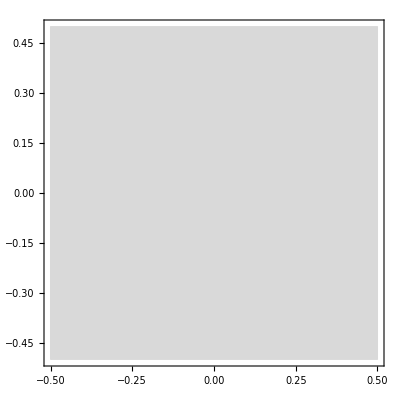

```mathematica
Export["/Users/Cem/Desktop/eigListsquare.csv",eigsquare,"CSV"];
```